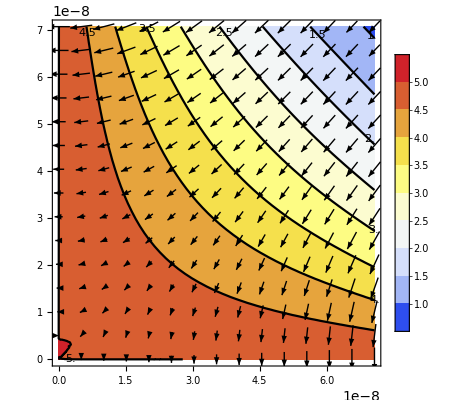

```mathematica
With[
{ϵ=10^(-3),R=10^(-7),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=150,n=100},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
(-1)*{
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

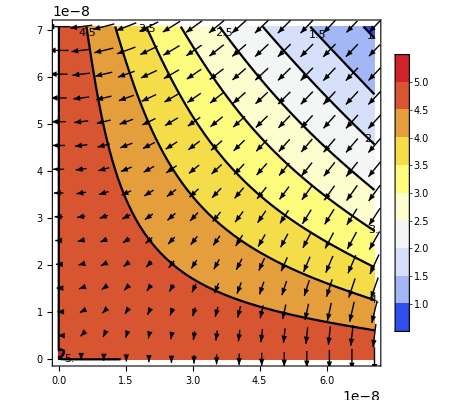

```mathematica
With[
{ϵ=10^(-3),R=10^(-7),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=150,n=200},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
(-1)*{
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```

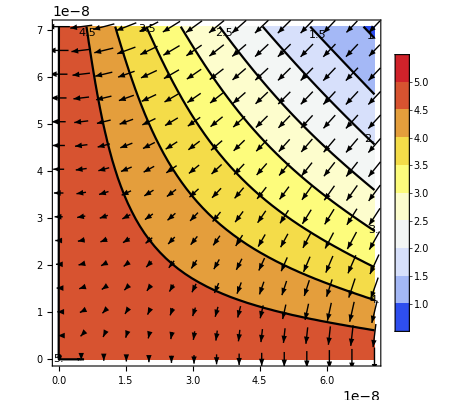

```mathematica
With[
{ϵ=10^(-3),R=10^(-7),q=1.6*10^(-19),ϕ0=5,ϵ0=8.85*10^(-12),M=150,n=500},
Show[
ContourPlot[
N[ϕ0+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m,m](1-Cos[m ArcTan[y/x]]-Tan[(m π)/(4+2ϵ)]Sin[m ArcTan[y/x]]),{m,1,M}]+If[0≤ArcTan[y/x]<π/4,1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Cos[m ArcTan[y/x]],{m,1,M}]),If[ArcTan[y/x]==π/4,q(Sqrt[2]-1)Log[2]/(8 n π ϵ0 R),1/n(1-Sqrt[(x^2+y^2)/R^2])^n (q/(8Sqrt[2]π ϵ0 R)+q/(4Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m (m+1)/4^(m+1)Binomial[2m+2,m+1]Tan[(m +1)π/(4+2ϵ)]Sec[m π/(2+ϵ)]Cos[m ArcTan[y/x]],{m,1,M}])]]],{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},PlotTheme->"Web",ColorFunction->"TemperatureMap",ContourLabels->All
],
VectorPlot[
(-1)*{
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-x+Sin[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])+Cos[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+
q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],x/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)/(n(Sqrt[x^2+y^2]-R)4^(m+1)R^m)(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1)π/(4+2ϵ)]Sec[m π/(2+ϵ)](-x Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))-m y Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]],
q/(4Sqrt[2]π ϵ0 R)Sum[(x^2+y^2)^(m/2-1)/(4R)^m m Binomial[2m,m](-y+Cos[m ArcTan[x,y]](y+x Tan[m π/(4+2ϵ)])-Sin[m ArcTan[x,y]](x-y Tan[m π/(4+2ϵ)])),{m,1,M}]+q/(4Sqrt[2]π ϵ0 R)If[0≤ArcTan[x,y]<π/4,y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}],y/(2R Sqrt[x^2+y^2])(1-Sqrt[x^2+y^2]/R)^(n-1)+Sum[(m+1)(x^2+y^2)^((m-3)/2)1/(n 4^(m+1)R^m (Sqrt[x^2+y^2]-R))(1-Sqrt[x^2+y^2]/R)^n Binomial[2m+2,m+1]Tan[(m+1) π/(4+2ϵ)]Sec[m π/(2+ϵ)](-y Cos[m ArcTan[x,y]](n(x^2+y^2)+m(x^2+y^2-R Sqrt[x^2+y^2]))+m x Sin[m ArcTan[x,y]](x^2+y^2-R Sqrt[x^2+y^2])),{m,1,M}]]
}
,{x,0,R/Sqrt[2]},{y,0,R/Sqrt[2]},VectorScale->{0.05,1,Automatic},PlotTheme->"GrayColor"
]
]
]
```